# Archimedes’ Hatbox — Hyperspherical Pseudorandom Vectors

Brian Beckman
December, 2023

## Abstract

Can we generate spherically symmetric uniform randoms starting with rectangularly symmetric, uniform randoms? Yes, but it takes care to do it efficiently. Rejection methods — generating rectangularly symmetric, uniform randoms and then throwing out those that are not in the d-ball — are crippled: only one in a trillion endpoints in the 27-cube is also in the 27-ball; the ratio gets worse exponentially as d increases. We need spherically symmetric uniform randoms in the thousands of dimensions for robots or even in the billions of dimensions for neural networks.

We exhibit two computational methods — one geometrical, the other statistical — that scale efficiently with d for generating pseudorandom vectors uniformly and symmetrically  on the surface and in the interior of the unit hypersphere of dimension d.

Though no method here is novel, descriptions available to me are unsatisfactory. The contributions of this note are proofs, executable specifications of algorithms, and numerical demonstrations.

## Definitions

The unit d-ball is the interior of a hypersphere, hyper meaning of any dimension. The unit d-ball is the set of all real d-vectors rooted at the origin, (x_1,x_2,…,x_d)∈ℝ^d, such that x_1^2+x_2^2+⋯+x_d^2<1. The unit d-sphere is the boundary of the d-ball, that is, the set of all real d-vectors such that x_1^2+x_2^2+⋯+x_d^2=1.

The unit d-cube is the set of all real d-vectors such that each coordinate is absolutely bounded by unity, inclusively, that is, where -1≤x_(i∈[1..d])≤1. The unit d-ball, d-sphere, and d-cube are also said to have radius 1, diameter 2.

We do not distinguish between the mathematical procedure of sampling a distribution and the computational procedure of generating pseudorandoms according to a distribution. Likewise, we do not distinguish between mathematical true randoms and computational pseudorandoms.

Generating randoms uniformly means the same as generating uniform randoms. Generating randoms symmetrically means the same as generating symmetric randoms. Symmetrically means independently of geometrical direction.

## Uniform Randoms in the d-Cube

Given an efficient method for generating uniform random scalars in the real interval [-1..1] — in the 1-cube — it is easy and efficient to generate rectangularly symmetric, uniform randoms in the d-cube: generate randoms for each of the d coordinate components independently.

Can we generate spherically symmetric uniform randoms starting with rectangularly symmetric, uniform randoms? Yes, but it takes care to do it efficiently. Rejection methods — generating rectangularly symmetric, uniform randoms and then throwing out those that are not in the d-ball — are crippled: only one in a trillion endpoints in the 27-cube is also in the 27-ball; the ratio gets worse exponentially as d increases.

Consider points (vector endpoints) uniformly distributed in the unit 2-cube, i.e., the unit square. The resulting (x,y) pairs are not uniform with angle, therefore not spherically symmetric. The following diagrams illustrate: here are points uniformly distributed in the 2-cube:

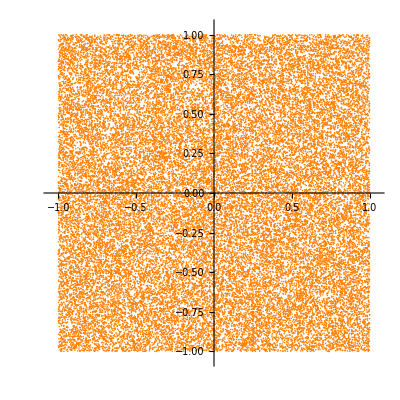

```mathematica
show2D$[points_,γ_:1.05]:=
ListPlot[Style[points,Orange],
PlotRange->{{-γ,γ},{-γ,γ}},
AspectRatio->1];
show3D$[points_,γ_:1.05]:=
ListPointPlot3D[Style[points,Orange],
PlotRange->{{-γ,γ},{-γ,γ},{-γ,γ}},
BoxRatios->{1,1,1}];
twoCubeRandoms$=
RandomVariate[
UniformDistribution[{{-1,1},{-1,1}}],
40000];
show2D$[twoCubeRandoms$]
```

There are too many points in the corners, at ArcTan[1,1]=0.7854, ArcTan[-1,1]=2.3562 and their negatives:

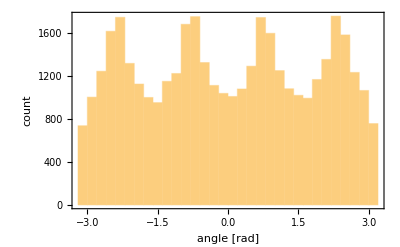

```mathematica
Histogram[MapThread[ArcTan,
{First/@twoCubeRandoms$,
First/@Rest/@twoCubeRandoms$}],
Frame->True,FrameLabel->{{"count",""},{"angle [rad]","Angle Distribution of \n40,000 Uniformly Random 2-Vectors"}}]
```

### Rejection Method: Impractical

We could reject, i.e., remove points in the unit d-cube that are not in the unit d-ball. Those would be points with radial component — Euclidean norm — greater than 1. However, rejection does not scale. As d grows, the number of corners goes up as 2^d and almost all points are in the corners, outside the d-ball. To see this this, consider the ratio of the volume of a unit d-ball to the volume of a unit d-cube.

What is the volume of a unit d-cube? Answer: 2^d. What is the volume of a unit d-ball? (see https://en.wikipedia.org/wiki/Volume_of_an_n-ball)

Answer for integer d:

```mathematica
ClearAll[vBall];
vBall[d_,r_:1]:=Piecewise[{{With[{k=d/2},π^k/(k!)r^d], Mod[d,2]===0}, {With[{k=(d-1)/2},(2k!(4π)^k)/(d!)r^d], Mod[d,2]===1}}];
Table[<|"dimension"->d,"ball volume"->vBall[d], "cube volume"->2^d,"cube/ball ratio"->N[2^d/vBall[d]]|>,{d,1,10}]//MatrixForm
```

(<|dimension→1,ball volume→2,cube volume→2,cube/ball ratio→1.|>
<|dimension→2,ball volume→π,cube volume→4,cube/ball ratio→1.27324|>
<|dimension→3,ball volume→(4 π)/3,cube volume→8,cube/ball ratio→1.90986|>
<|dimension→4,ball volume→π^2/2,cube volume→16,cube/ball ratio→3.24228|>
<|dimension→5,ball volume→(8 π^2)/15,cube volume→32,cube/ball ratio→6.07927|>
<|dimension→6,ball volume→π^3/6,cube volume→64,cube/ball ratio→12.3846|>
<|dimension→7,ball volume→(16 π^3)/105,cube volume→128,cube/ball ratio→27.0913|>
<|dimension→8,ball volume→π^4/24,cube volume→256,cube/ball ratio→63.0742|>
<|dimension→9,ball volume→(32 π^4)/945,cube volume→512,cube/ball ratio→155.222|>
<|dimension→10,ball volume→π^5/120,cube volume→1024,cube/ball ratio→401.543|>)

for arbitrary real dimensions, the plot must be logarithmic to be useful. Notice the volume ratio is about 10^-12 for d=27.

```mathematica
ClearAll[vBall];
vBall[d_,r_:1]:=(π^(d/2)r^d)/Gamma[1+d/2];
```

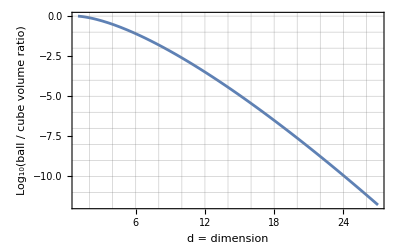

```mathematica
Plot[Log10[vBall[d]/2^d],{d,1,27},
Frame->True,GridLines->All, FrameLabel->{{"Log_10(ball / cube volume ratio)",""},{"d = dimension","Volume Ratio of Unit d-ball to Unit d-cube"}}]
```

The ratio of ball-to-cube volume in 27 dimensions is one trillionth, so the rejection method generates a trillion times more points than it keeps. The computer does 1 trillion times more work than it ought to do. Rejection is impractical for even moderately large d.

## Radial Symmetry

Observe that a multivariate Gaussian or multinormal distribution is radially symmetric. Sampling x from (ⅇ^(-x^2/2))/(√(2 π)), and y similarly, then noticing that x and y are independent (the probability of their occurring simultaneously is the product of their individual probabilities), we get (ⅇ^(-x^2/2))/(√(2 π))×(ⅇ^(-y^2/2))/(√(2 π))=(ⅇ^(-1/2 (x^2+y^2)))/(2 π). A similar construction extends to any number of dimensions.

The multinormal distribution is radially symmetric because it depends only on the radius squared, x^2+y^2, not on the azimuth angle. But it is not radially uniform, as the following figure demonstrates:

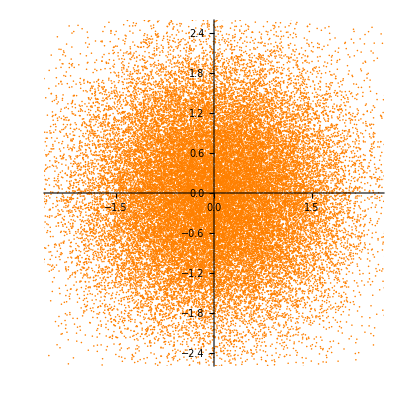

```mathematica
show2D$[RandomVariate[
MultinormalDistribution[IdentityMatrix[2]],40000],2.5]
```

## Radial Uniformity

Due to radial symmetry, normalized d-vectors from the d-ball (interior) are uniform on the d-sphere (surface). For example, the following points are uniformly distributed on the 2-sphere:

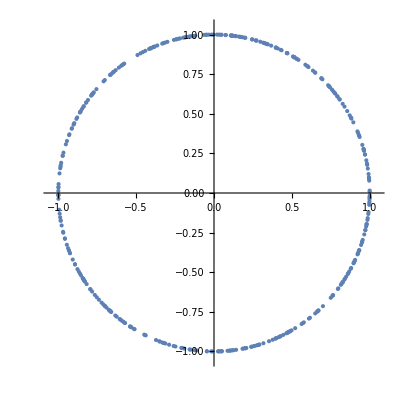

```mathematica
With[{γ=1.05},
ListPlot[Normalize/@
RandomVariate[
MultinormalDistribution[IdentityMatrix[2]],400],
PlotRange->{{-γ,γ},{-γ,γ}},AspectRatio->1]]
```

## From Symmetry to Uniformity

Now that we can generate uniform randoms on the d-sphere, the boundary of the d-ball, can we fill the interior uniformly? We show below two ways: a geometrical construction and a statistical construction.

## Efficient Geometrical Construction

Shrink vectors radially, pulling their end-points toward the center, preserving radial symmetry. But my how much to shrink them? Shrinking by a uniform random scalar factor in [0,1] will not work. The results will be too sparse in outer zones and too dense in inner zones:

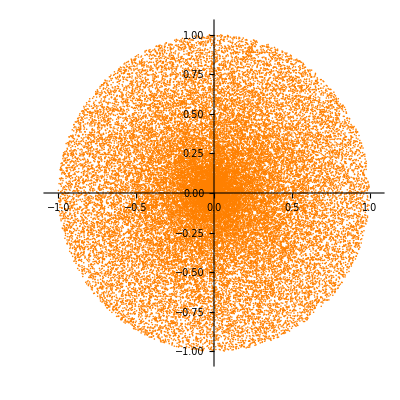

```mathematica
show2D$@With[{count=40000},With[{pointsOnSphere=
Normalize/@
RandomVariate[
MultinormalDistribution[IdentityMatrix[2]],count],
scalar=
RandomVariate[UniformDistribution[{0,1}],count]},
MapThread[Times,{pointsOnSphere,scalar}]]]
```

If points were uniformly distributed with radius r, the volume density would be proportional to r^-d=1/r^d, approaching infinity as r→0. If points were uniformly distributed in r^(1/d), then the volume density would be constant: that is what we want. The following is code we re-use in the rest of this note.

### sampleDBall

```mathematica
ClearAll[sampleDBall];
sampleDBall[d_,n_]:=
With[{
pointsOnSphere=
Normalize/@
RandomVariate[
MultinormalDistribution[IdentityMatrix[d]],n],
scalar=
Power[
RandomVariate[UniformDistribution[],n],
1/d]},
MapThread[Times,{pointsOnSphere,scalar}]];
```

The following plots illustrate points uniformly distributed in radius in two and three dimensions, and thus uniformly distributed in the 2-ball and in the 3-ball, respectively:

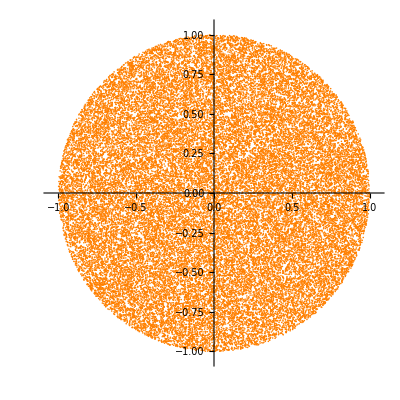

```mathematica
show2D$[sampleDBall[2,40000]]
```

```mathematica
show3D$[sampleDBall[3,40000]]
```

-Graphics3D-

## Uniformity Statistics

It’s well and good to appear to be uniform, but we must demonstrate uniformity with statistics.

We exhibit two ways to collect uniformity statistics from a sample: by shell and by cubie. From the statistics, we can calculate average point density (per unit d-volume) and check that it is uniform. The shell method counts points that lie within d-shells of constant volume. The cubie method counts points in elementary d-cubes of constant volume. The shell method is robust and practical because it is easy to construct shells of accurately and non-infinitesimal constant volume. The cubie method is obvious and intuitive, but inaccurate and impractical for dimensions more than three. Accurate statistics require a large number of small cubies, but practical statistics requires a small number of large cubies. Large cubies cross the boundary of a ball too often — a discretization artifact. Cubies that cross the boundaries of the ball have deficient counts: below the mean. The distribution of cubie counts quickly becomes skewed to the small tail as d increases. Skewed statistics don’t fit a uniform distribution — a Gaussian — and fail a Chi-squared test for no decent reason. The rest of this section demonstrates.

### Shell Statistics

The volume of a d-ball of radius ρ is proportional to ρ^d. Incrementing ρ^d by integer multiples of a macroscopic constant Δv produces a sequence of shells of equal volumes (constant Δv is proportional to constant Δ-volume). Thus, we may index shells by integer multiples of Δv: shell number Ceiling[ρ^d,Δv] contains the point p with Euclidean norm ρ.

In a large sample, we expect the mean number of vectors with endpoints in each shell to be drawn from the same, uniform distribution with constant mean μ and standard deviation √μ. The Chi-squared test for a uniform distribution demands that the standard deviation of endpoint counts in each shell be approximately equal to √μ. That observation gives us a pragmatic, “eyeball” test for uniformity. If μ is not constant or if the standard deviation is unreasonably far from √μ, we likely have a non-uniform source distribution.

The following are numerical statistics across 100 shells of equal volume for 1000000 spherically uniform randoms in each of two, three, six, sixteen, and 276 dimensions. The expected mean number of points in each shell is 10000=1000000/100, and the expected standard deviations of the counts is √10000=100. The empirical standard deviations agree reasonably well with the expected.

A rigorous Chi-squared test would give the probability that each shell is not drawn from the same uniform distribution. The “eyeball” agreement between empirical and expected standard deviations is good enough that a rigorous Chi-squared test does not seem worth the effort.

### Sampled Shell Counts

```mathematica
ClearAll[pairwise];
pairwise[fn_,list_List]:=
MapThread[fn,{Drop[list,-1],Rest[list]}];

ClearAll[pointsInShell2];
pointsInShell2[points_,d_,dr_]:=
GroupBy[points,p↦Ceiling[Norm[p]^d,dr]];

ClearAll[sampledShellCounts2];
sampledShellCounts2[deltaR_:0.01,d_:2,n_:4000,sampler_:sampleDBall]:=
With[{points=sampler[d,n]},
With[{countsAssoc=Length/@pointsInShell2[points,d,deltaR]},
Values[countsAssoc]]];

ClearAll[countsStats];
countsStats[counts_]:=
With[{𝒟=counts},
With[{
tot=Plus@@𝒟,
μ=Mean@𝒟,
σ=N@StandardDeviation@𝒟,
min=Min[𝒟],
max=Max[𝒟],
P=Quiet@FindDistribution[𝒟]},
Column@{ListLinePlot[𝒟,PlotRange->Full,ImageSize->Medium,AxesLabel->{"Sample Id","Sampled Number of Counts"}],
Show[
Histogram[𝒟,Automatic,"PDF",PlotRange->Full,AxesLabel->"Distribution of Sampled Number of Counts"],
Plot[PDF[P,c],{c,min,max}],ImageSize->Medium],
<|"actual == expected μ"->N@μ,"expected stddev"->N@Sqrt[μ],"n samples"->Length[counts],"actual stddev"->σ,"total"->tot,"min"->min,"max"->max|>}]];
```

#### Two Dimensions

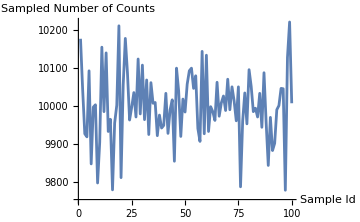
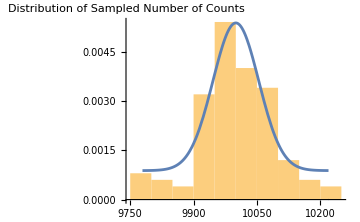
-Graphics-
-Graphics-
<|actual == expected μ→10000.,expected stddev→100.,n samples→100,actual stddev→90.0325,total→1000000,min→9779,max→10220|>

```mathematica
countsStats[sampledShellCounts2[0.01,2,1000000]]
```

#### Three Dimensions

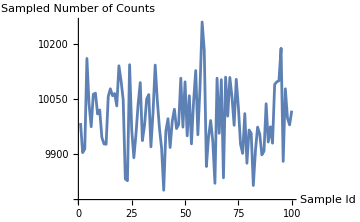
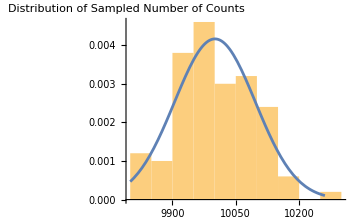
-Graphics-
-Graphics-
<|actual == expected μ→10000.,expected stddev→100.,n samples→100,actual stddev→91.5347,total→1000000,min→9800,max→10261|>

```mathematica
countsStats[sampledShellCounts2[0.01,3,1000000]]
```

#### Six Dimensions

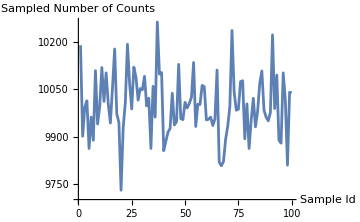
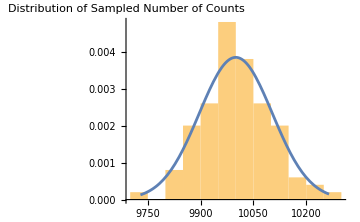
-Graphics-
-Graphics-
<|actual == expected μ→10000.,expected stddev→100.,n samples→100,actual stddev→98.1884,total→1000000,min→9729,max→10265|>

```mathematica
countsStats[sampledShellCounts2[0.01,6,1000000]]
```

#### Sixteen Dimensions

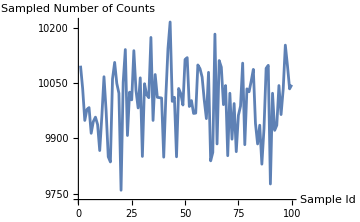
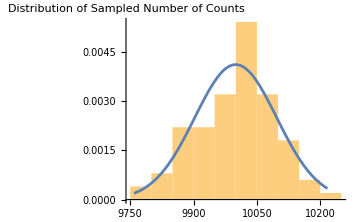
-Graphics-
-Graphics-
<|actual == expected μ→10000.,expected stddev→100.,n samples→100,actual stddev→93.1243,total→1000000,min→9759,max→10217|>

```mathematica
countsStats[sampledShellCounts2[0.01,16,1000000]]
```

#### 276 Dimensions

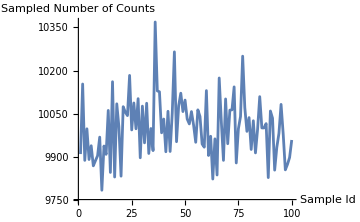
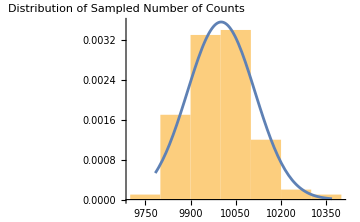
-Graphics-
-Graphics-
<|actual == expected μ→10000.,expected stddev→100.,n samples→100,actual stddev→105.353,total→1000000,min→9783,max→10369|>

```mathematica
countsStats[sampledShellCounts2[0.01,276,1000000]]
```

### Cubie Statistics

Statistics by cubie ignore geometry and count points in an evenly-spaced Cartesian grid. Statistics by cubie do not scale to large d, where almost all the volume contains empty cubies. Accurate statistics require an astronomically impractical number of small cubies. However, statistics by cubie are instructive for small d, illustrating indexing by hashing cubie coordinates in a Mathematica Association, similar to a Python dictionary or to a Clojure hashmap.

Find the integer cubie boundaries for a cubie size δ via Floor and Ceiling near a point x. Boundary tuples are the keys of the hash table. Every point within a certain cubie hashes to the same key.

```mathematica
ClearAll[cellBoundaryTuple];
cellBoundaryTuple[x_,δ_]:=
With[{f=Floor[x,δ],c=Ceiling[x,δ]},
{f,c}];
```

Make a function of an existing hash table and a point, closed over a given cubie size δ. Locate the cubie of the point in the hash table and increment the cubie’s counts.

```mathematica
ClearAll[makeCubifer];
makeCubifer[δ_]:=
Function[{dict,point},
Module[{temp=dict},
With[{key=cellBoundaryTuple[point,δ]},
With[{val=temp[key]},
With[{test=Head[val]},
If[Missing===test,
AssociateTo[temp,key->1],
temp[key]++]]]];
temp]];
```

Visualize cubie densities — red for small densities, indigo for large. Notice the densities are all reddish on the boundary of the hypersphere. That’s where cubies cross the boundary and counts are deficient for no decent reason. That fact is going to kill the cubie method as dimensions grow. We could correct the deficiency by an elaborate geometrical analysis, but it’s a lot of algebraic work and not justified because we have a good shell algorithm. It would be an interesting exercise, especially for any d.

```mathematica
ClearAll[cubiePolygon];
Module[{},
cubiePolygon[{xyLeft_,xyRight_},value_,maxVal_,minVal_]:=
With[{xLeft=xyLeft[[1]],xRight=xyRight[[1]],
yBottom=xyLeft[[2]],yTop=xyRight[[2]]},
{Hue[(value-minVal)/(maxVal-minVal)],Polygon[{{xLeft,yBottom},{xRight,yBottom},
{xRight,yTop},{xLeft,yTop}}]}]];
ClearAll[illustrateCubifers];
illustrateCubifers[δR_:0.1,d_:2,n_:4000]:=
With[{sample=sampleDBall[d,n]},
With[{kvs=Fold[makeCubifer[δR],<||>,sample]},
With[{keys=Keys[kvs],values=Values[kvs]},
With[{cubieArea=Times@@(keys[[1,2]]-keys[[1,1]])},
With[{density=values/cubieArea},
Print[<|"values"->Short[values],"sum"->Plus@@values, 
"number of cubies"->Length[keys],"cubie area"->cubieArea,
"point densities per cubie"->Short[density],
"avg point density"->Mean[density],
"stddev point density"->StandardDeviation[density]|>];
With[{vx=Max[values],vn=Min[values],len=Length[values]},
MapThread[cubiePolygon,{keys,values,
ConstantArray[vx,len],
ConstantArray[vn,len]}]]]]]]]
```

<|values→{25,28,24,33,31,42,24,32,«3232»,1,1,2,1,3,1,1},sum→100000,number of cubies→3247,cubie area→0.001,point densities per cubie→{25000.,«3245»,1000.},avg point density→30797.7,stddev point density→7177.66|>

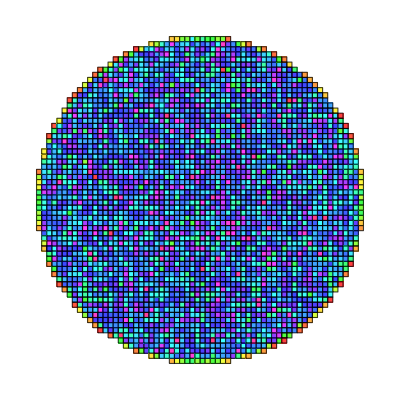

```mathematica
Graphics[{Opacity[0.75],EdgeForm[Black],illustrateCubifers[0.001^(1/2),2,100000]}]
```

The following function computes the counts and reports empirical sample statistics for any d, any δR, and any n.

```mathematica
ClearAll[sampledCubieCounts];
sampledCubieCounts[δR_:0.1,d_:2,n_:4000]:=
Module[{volumeRatio=N[vBall[d]/2^d]},
Module[{pointDensityInTheBall=N[n/vBall[d]]},
Print[<|"Total number of cubies, δR^-d"->δR^-d,"d-ball volume / d-cube volume"->volumeRatio,
"number of cubies in the ball"->δR^-d volumeRatio,"Theoretical point density in the ball"->pointDensityInTheBall,
"Theoretical overall mean points per cubie"->pointDensityInTheBall/δR^-d|>];
Module[{cubieHash=Fold[makeCubifer[δR],<||>,sampleDBall[d,n]]},
Print[<|"Number of hash keys"->Length@Keys[cubieHash],"sum of counts in all cubies"->Plus@@Values[cubieHash]|>];
Values[cubieHash]]]];
```

In the following demonstrations, we consider n=100000 vector endpoints, restricting the sizes of cubies to the d-th root of 0.001 so that the total number of cubies is 1000; any more and the simulations are uncomfortably slow. The number of hash keys is much larger than the real-number fraction of cubies inside the ball because hash keys include cubies with deficient counts — cubies crossing the boundary. The proportion of cubies with deficient counts grows quickly with d because the relative size of cubies to the size of the ball grows quickly with d. This is a discretization effect. Also notice that Mathematica cannot find a smooth fit to the statistics even for small d. Unlike shell statistics, the plots show no smooth curve because Mathematica’s FindDistribution fails. That’s why we wrap it in Quiet in the code for countsStats.

#### Two Dimensions

<|Total number of cubies, δR^-d→1000.,d-ball volume / d-cube volume→0.785398,number of cubies in the ball→785.398,Theoretical point density in the ball→31831.,Theoretical overall mean points per cubie→31.831|>

<|Number of hash keys→3247,sum of counts in all cubies→100000|>

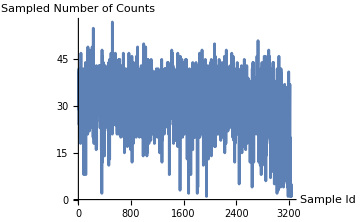
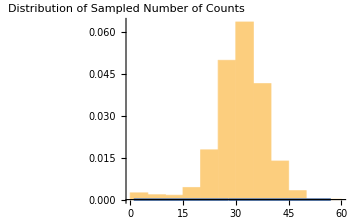
-Graphics-
-Graphics-
<|actual == expected μ→30.7977,expected stddev→5.54956,n samples→3247,actual stddev→7.23426,total→100000,min→1,max→57|>

```mathematica
countsStats[sampledCubieCounts[0.001^(1/2),2,100000]]
```

There are already, even in two dimensions, a noticeable number of deficiently populated cubies (the tail to the left of the peak above). These are the cubies crossing the circle and in the corners outside the circle.

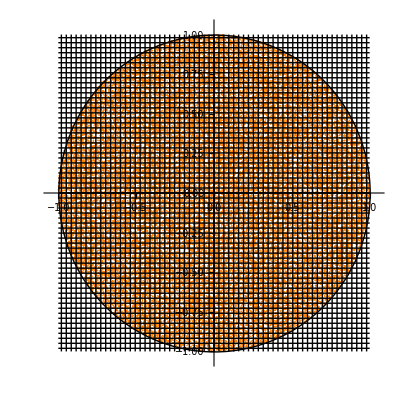

```mathematica
Show[show2D$[sampleDBall[2,40000]],Graphics[Circle[]],
Graphics@Line[{{#,-1},{#,1}}]&/@Range[0,1,0.001^(1/2)],
Graphics@Line[{{-1,#},{1,#}}]&/@Range[0,1,0.001^(1/2)],
Graphics@Line[{{#,-1},{#,1}}]&/@Range[0,-1,-0.001^(1/2)],
Graphics@Line[{{-1,#},{1,#}}]&/@Range[0,-1,-0.001^(1/2)]]
```

#### Three Dimensions

<|Total number of cubies, δR^-d→1000.,d-ball volume / d-cube volume→0.523599,number of cubies in the ball→523.599,Theoretical point density in the ball→23873.2,Theoretical overall mean points per cubie→23.8732|>

<|Number of hash keys→4832,sum of counts in all cubies→100000|>

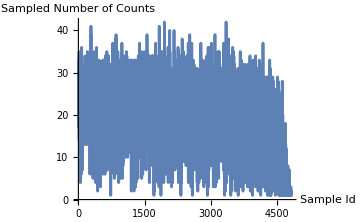
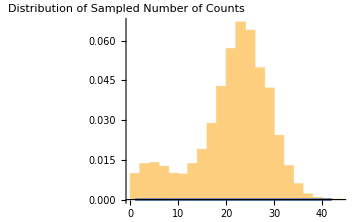
-Graphics-
-Graphics-
<|actual == expected μ→20.6954,expected stddev→4.54922,n samples→4832,actual stddev→7.88107,total→100000,min→1,max→42|>

```mathematica
countsStats[sampledCubieCounts[0.001^(1/3),3,100000]]
```

In three dimensions, the number of deficient cubies is larger than “noticeable.”

#### Six Dimensions

<|Total number of cubies, δR^-d→1000.,d-ball volume / d-cube volume→0.0807455,number of cubies in the ball→80.7455,Theoretical point density in the ball→19350.9,Theoretical overall mean points per cubie→19.3509|>

<|Number of hash keys→11932,sum of counts in all cubies→100000|>

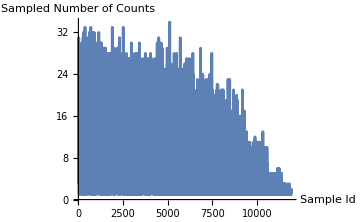
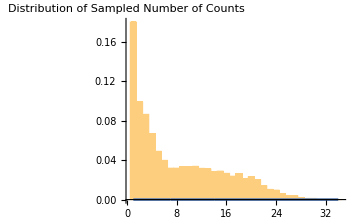
-Graphics-
-Graphics-
<|actual == expected μ→8.38082,expected stddev→2.89497,n samples→11932,actual stddev→7.10677,total→100000,min→1,max→34|>

```mathematica
countsStats[sampledCubieCounts[0.001^(1/6),6,100000]]
```

In six dimensions, the deficient cubies dominate the statistics.

#### Twenty-Seven Dimensions

<|Total number of cubies, δR^-d→1000.,d-ball volume / d-cube volume→1.66053×10^-12,number of cubies in the ball→1.66053×10^-9,Theoretical point density in the ball→4.48688×10^8,Theoretical overall mean points per cubie→448688.|>

<|Number of hash keys→99964,sum of counts in all cubies→100000|>

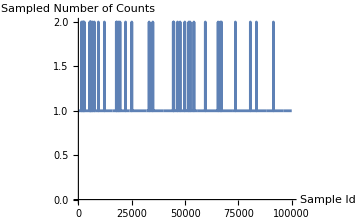
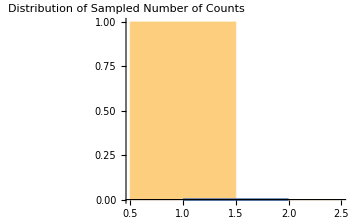
-Graphics-
-Graphics-
<|actual == expected μ→1.00036,expected stddev→1.00018,n samples→99964,actual stddev→0.0189738,total→100000,min→1,max→2|>

```mathematica
countsStats[sampledCubieCounts[0.001^(1/27),27,100000]]
```

In twenty-seven dimensions, virtually all the cubies are deficient.

There is no point in examining larger dimensions. To find cubies with populations greater than 1 (statistically), we must reduce the sizes of cubies, and thus increase their number and the computation time exponentially with d. It is not worth the computation time. We already have the shell method for verifying uniformity.

## Efficient Statistical Construction

Alternatively to the geometrical constructions above, sample uniformly on the (d+2)-sphere (not in the (d+2)-ball), then delete any two coordinates of each point, deterministically or at random. We derive and prove his surprising procedure via Archimedes’ Hatbox Theory.

We already know how to sample uniformly on the (d+2)-sphere: normalized multinormals. The following code illustrates generating uniforms in the 1-ball from uniforms on the 3-sphere by dropping two, randomly chosen coordinates:

```mathematica
ClearAll[sampleDBall2];
sampleDBall2[d_,n_,e_:2]:=
RandomSample[#,e]&/@(* random rejection *)
Normalize/@ (* uniform on the d-sphere *)
RandomVariate[
MultinormalDistribution[IdentityMatrix[d+e]],n];
```

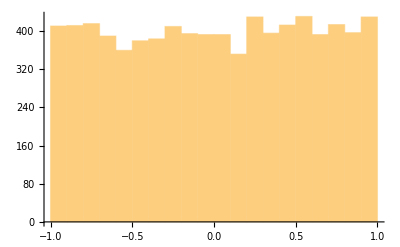

```mathematica
Histogram[Flatten[sampleDBall2[1,4000,2]]]
```

Why does this work? Why reject two coordinates at random, instead of one or three or seventeen?

First, realize that dropping one coordinate at random is the same as dropping the same coordinate from every point, at least for calculating the distribution of points, because all coordinates are sampled from the same random distribution. Henceforth, we always drop the last two coordinates, z and y.

### Theorem 1

The d-volume density of points is constant in the d-sphere after projecting out z and y from a distribution constant per unit (d+2)-hyperspherical area.

### Proof

We prove the theorem first for three dimensions, then argue by extension to dimensions greater than three.

Plan: In 3D, produce a 2D distribution of points by dropping z. Next, drop the y coordinate by integrating it to produce a 1D density. Prove the resulting 1D density of points per unit of the x axis is independent of x.

As before, generate spherically uniform 3-vectors of unit length — on the 3-sphere — by sampling the 3-dimensional multinormal distribution, then normalizing the vectors:

```mathematica
show3D$[threeDPoints$=
Normalize/@
RandomVariate[
MultinormalDistribution[IdentityMatrix[3]],
40000]]
```

-Graphics3D-

Drop the z (last) coordinate of each point to produce a radially symmetric but non-uniform distribution in the 2-ball:

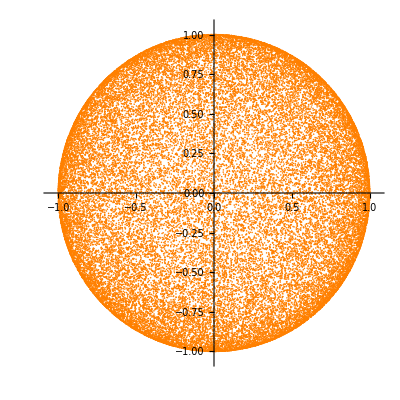

```mathematica
show2D$[(twoDPoints$=Drop[#,-1]&/@threeDPoints$)]
```

What is the 2D distribution at this step?

#### Lemma 1

The 2D density of points is proportional to 1/√(1-r^2), where r<1 is the 2D distance from the origin. The density is unity near the origin and approaches infinity as r⟶1.

Consider curved belts (or spherical segments) of equal z-height h on the surface of the unit 3-sphere surrounding the z axis. Each such belt has equal surface area 2π h by Archimedes' Hatbox Theorem (also see Apostol, T., Mnatsakanian, M. (2004). A fresh look at the method of Archimedes. Am. Math. Monthly 111: 496–508. doi.org/10.2307/4145068, for much more.)

The following illustrates five belts in 3D:

```mathematica
Graphics3D[With[{dh=0.005,n=5,o={0,0,0}},
{Opacity[0.25],Sphere[],
Cone[{{0,0,#+dh},o},√(1-#^2)]&/@Range[0,1,1./n],
Cylinder[{o,{0,0,#+dh}},√(1-#^2)]&/@Range[0,1,1./n]}]]
```

-Graphics3D-

##### Proof of the Hatbox Theorem

The next diagram shows a longitudinal cross-section of the 3-ball with belts of equal z-height.

A belt of z-height h corresponds to two elevation angles, θ_1<θ_2, such that sin θ_2-sin θ_1=h.

A differential element of area on the surface, in co-spherical coordinates, (θ (elevation),ϕ (azimuth)), via elevation (co-latitude) angles θ rather than the usual latitude angles, is cos θ dϕ dθ. The area of a belt is

```mathematica
∫_0^(2π) ∫_Subscript[θ, 1]^Subscript[θ, 2] Cos[θ]ⅆθⅆϕ
```

2 π (-Sin[θ_1]+Sin[θ_2])

which is 2πh.

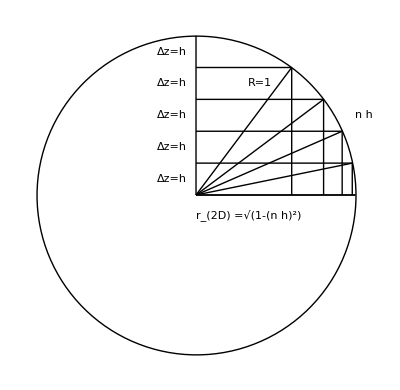

```mathematica
With[{o={0,0},N=5},
Graphics[{Circle[],
Text[Δz=h,{-0.15,#+0.5/N}]&/@Range[0,.99,1./N],
Text[n h,{1.05,0.5}],
Text[Subscript[r, 2D] =√(1-(n h)^2),{0.33,-.125}],
Text[R=1,{0.4,0.70}],
Line[{{0,#},{√(1-#^2),#}}&/@Range[0,.99,1./N]],
Line[{{√(1-#^2),0},{√(1-#^2),#}}&/@Range[0,.99,1./N]],
Line[{o,{√(1-#^2),#}}]&/@Range[0,1,1./N]}]]
```

QED Hatbox Theorem ■

Back to lemma 1. The belts projected in 2D form annuli, or rings. Consider the following projection of belts of z-height h=0.1 onto the 2D plane, along with the sample points, with their z coordinates dropped:

```mathematica
ClearAll[annuli];
annuli=Graphics@Circle[{0,0},√(1-#^2)]&/@Range[0,1,0.1];
Show[{show2D$[twoDPoints$]}~Join~annuli]
```

-Graphics-

We claim that each annulus contains the same number of points, statistically.

The following illustrates a grouping function that isolates points in each annulus and shows a selection of one such group, the one whose maximum z-height is 0.8:

```mathematica
ClearAll[twoDPointsGroupedInAnnuli];
twoDPointsGroupedInAnnuli=GroupBy[twoDPoints$,Ceiling[√(1-Norm[#]^2),0.1]&];
Show[{show2D$[twoDPointsGroupedInAnnuli[0.8]]}~Join~annuli]
```

-Graphics-

The following illustrates that all annuli have, statistically, the same numbers of points.

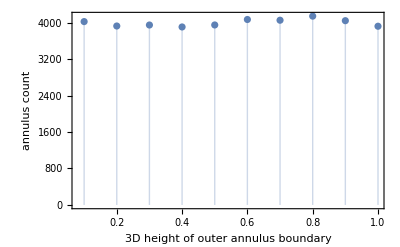

```mathematica
ListPlot[Length/@twoDPointsGroupedInAnnuli,
Filling->Axis,
PlotRange->{All,{0,All}},
Frame->True,
FrameLabel->{
{"annulus count",""},
{"3D height of outer annulus boundary","Annulus Count as a Function of Cell["z",ExpressionUUID->"7aba8c8e-68bd-48ae-be25-02e29bfdbf3b"]-height"}}]
```

The following illustrates the 2D widths and 2D areas of the annuli as a function of z-height:

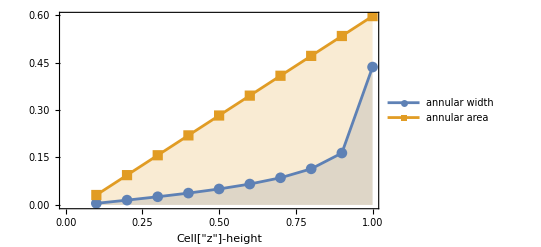

```mathematica
ListLinePlot[
With[{zs=Range[0,1,0.10]},
With[{rs=√(1-#^2)&/@zs},
{{Rest@zs,pairwise[#1-#2&,rs]}ᵀ,
{Rest@zs,pairwise[π(#1^2-#2^2)&,rs]}ᵀ}]],
Frame->True,PlotMarkers->Automatic,
FrameLabel->{{"",""},{"Cell["z",ExpressionUUID->"24788e15-f272-47aa-b6ab-08090297566e"]-height","Annular width and area versus Cell["z",ExpressionUUID->"e5418a73-8752-4334-9693-fb710b0b183d"]-height"}},
Filling->Axis,
PlotLegends->{"annular\nwidth","annular\narea"}]
```

Annular area is linear with z-height, and z-height varies as √(1-r^2). Point count per annular area is constant with z-height, so 2D point density against 2D r varies as 1/√(1-r^2). We use that fact in the integral below.

QED Lemma 1 ■

Slice the circle vertically into bands of equal width Δx and y-height √(1-x^2):

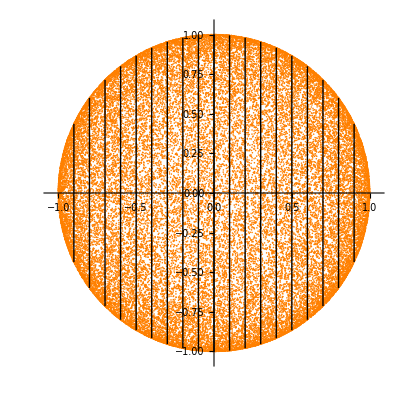

```mathematica
Show[{show2D$[twoDPoints$]}~Join~
(With[{y=√(1-#^2)},
Graphics@Line[{{#,-y},{#,y}}]]&/@Range[-1,1,0.1])]
```

Eliminate y by integrating the density over a particular band at position x and invoke lemma 1 for the density 1/√(1-r^2)=1/√(1-y^2-x^2):

```mathematica
∫_(-√(1-x^2))^(√(1-x^2)) 1/(√(1-y^2-x^2))ⅆy
```

ConditionalExpression[π, -1<Re[x]<1&&Im[x]==0]

independent of x.

Therefore each band has the same density.

There follow statistics for sampling 1,000,000 points according to this scheme of rejecting two coordinates for two dimensions and for 276 dimensions. As before, with a uniform distribution, we expect the standard deviations of counts to vary as the square root, 100, of the mean of the 10000 points in each annulus — the “eyeball” Chi-squared test for a uniform distribution.

### Two Dimensions

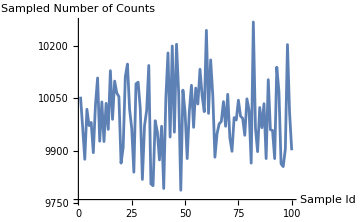
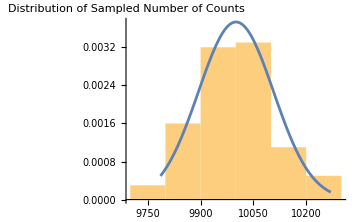
-Graphics-
-Graphics-
<|actual == expected μ→10000.,expected stddev→100.,n samples→100,actual stddev→102.821,total→1000000,min→9786,max→10270|>

```mathematica
countsStats[sampledShellCounts2[0.01,2,1000000,sampleDBall2]]
```

### 276 Dimensions

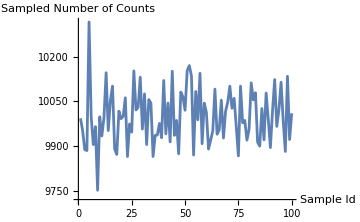
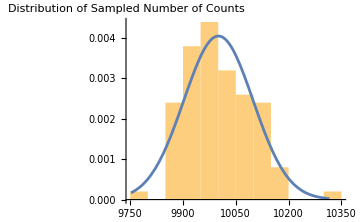
-Graphics-
-Graphics-
<|actual == expected μ→10000.,expected stddev→100.,n samples→100,actual stddev→91.4368,total→1000000,min→9752,max→10316|>

```mathematica
countsStats[sampledShellCounts2[0.01,276,1000000]]
```

To extend the theorem to more dimensions, let x^2 stand for the Euclidean norm of all dimensions other than the last two. The integral still does not depend on x.

QED Theorem 1 ■